# Final Exam Review

## Computer Graphics, Wolfram Mathematica

```mathematica
(* Songkran Challenge *)
```

```mathematica
Clear[obj1]
```

```mathematica
r1=2;
color1=RandomColor[5]; color2=RandomColor[5];
points1[t_]:={r1*Cos[10*t],r1*Sin[10*t],t}
obj1[t_,c_]:=ParametricPlot3D[{u,v,u^2+v^2}+points1[t],{u,-1,1},{v,-1,1},PlotStyle->c]
Manipulate[Show[ParametricPlot3D[points1[t1],{t1,0,2*Pi},PlotStyle->c1,PlotRange->{{-3,3},{-3,3},{-1,8}},Axes->True],obj1[t2,c2]],{t2,0,2*Pi},{c1,color1,ControlType->PopupMenu},{c2,color2}]
```

```mathematica
path2graphic[c_]:=ParametricPlot3D[points1[t1],{t1,0,2*Pi},PlotStyle->c][[1]];
obj2graphic[t_,c_]:=ParametricPlot3D[{u,v,u^2+v^2}+points1[t],{u,-1,1},{v,-1,1},PlotStyle->c][[1]]
Manipulate[Graphics3D[GeometricTransformation[{path2graphic[c1],obj2graphic[(5+t)/10*2*Pi,c2]},TranslationTransform[{t,0,0}]],PlotRange->{{-8,8},{-3,3},{-1,8}},Axes->True],{t,-5,5},{c1,color1},{c2,color2}]
```

```mathematica
Interp3D[data_]:=Module[{x,y,z,fx,fy,fz},
x=Transpose[data][[1]];
y=Transpose[data][[2]];
z=Transpose[data][[3]];
fx=Interpolation[x];
fy=Interpolation[y];
fz=Interpolation[z];
traj={fx[#1],fy[#1],fz[#1]}&;
traj]
```

```mathematica
data6={{-4,2,4},{4,5,-1},{2,5,0},{1,1,3},{2,-6,-6},{-4,-4,-4},{0,0,0},{0,0,0},{1,5,0},{1,1,3},{1,-1,-1},{2,2,2}};
L6=Dimensions[data6][[1]];
```

```mathematica
MoveF6[F_,data_,ColorS_,ColorT_,R1_]:=Module[{t1,SurfacePosF,plottraj,plotpoints,plotF1,plotF,Object},
plottraj=ParametricPlot3D[Interp3D[data6][t1],{t1,1,L6},PlotStyle->ColorT];
Object[t1_]:={Red,F[traj[t1],R1]};
plotF[t1_]:=Graphics3D[Object[t1]];
plotF1[t1_]:=Show[{plotF[t1],plottraj},PlotRange->7.5];
plotF1]
```

```mathematica
{Manipulate[MoveF6[Sphere,data6,Red,Blue,1.5][td],{td,1,L6}],
Table[MoveF6[Sphere,data6,Red,Blue,1.5][i],{i,1,12,4}]}
```

{,{-Graphics3D-,-Graphics3D-,-Graphics3D-}}

```mathematica
(* Prime *)
```

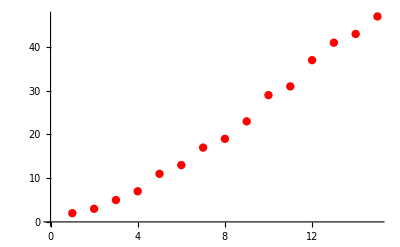
{{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47},-Graphics-}

```mathematica
PrimePlot[from_,to_]:=Module[{i,plot,T},
T=Table[If[PrimeQ[i],i,Nothing],{i,from,to,1}];
plot=ListPlot[T,PlotStyle->{Red,PointSize[0.015]}];
{T,plot}]
PrimePlot[1,50]
```

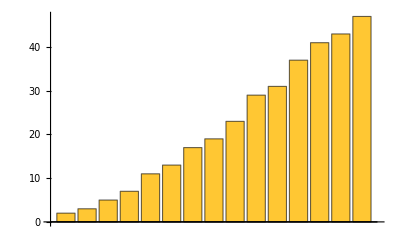
{{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47},-Graphics-}

```mathematica
PrimeBar[from_,to_]:=Module[{i,plot,T},
T=Table[If[PrimeQ[i],i,Nothing],{i,from,to,1}];
plot=BarChart[T];
{T,plot}]
PrimeBar[1,50]
```

```mathematica
PrimeCount[to_]:=Module[{i,T},
T=Table[If[PrimeQ[i],i,Nothing],{i,1,to,1}];
Length[T]]
```

```mathematica
PrimeList=ListPlot[Table[{i,PrimeCount[i]},{i,1,100}],PlotStyle->{Red,PointSize[0.015]}];
```

```mathematica
PrimePoints=Table[{i,PrimeCount[i]},{i,{1,25,50,75,100}}]
```

{{1,0},{25,9},{50,15},{75,21},{100,25}}

```mathematica
PrimeFnc=Interpolation[PrimePoints,Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
PrimeGraph=Plot[PrimeFnc[t],{t,1,100}];
```

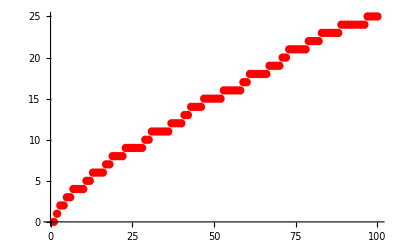
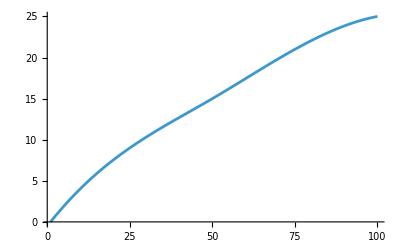
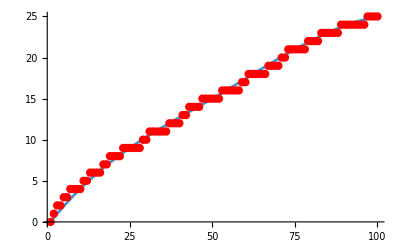

```mathematica
{PrimeList,PrimeGraph,Show[{PrimeGraph,PrimeList}]}
```

```mathematica
(* Which, Exclusion *)
```

```mathematica
r4=3;
f1[t_]:={r4*Cos[t],r4*Sin[t]+r4} 
f2[t_]:={t,r4}
f3[t_]:={r4*Cos[t]+r4+3*Pi,r4*Sin[t]+r4}
```

```mathematica
path4[t_]:=Which[
t>=0&&t<=2*Pi,f1[t],
t>2*Pi&&t<3*Pi,f2[t],
t>=3*Pi,f3[t]]
```

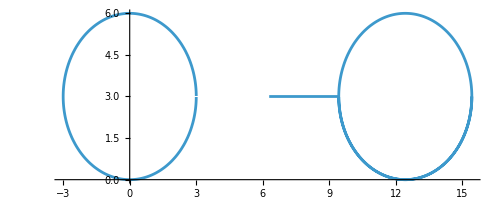
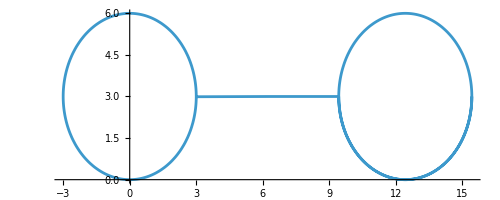

```mathematica
{ParametricPlot[path4[t],{t,0,6*Pi}],
objpath4=ParametricPlot[path4[t],{t,0,6*Pi},Exclusions->None]}
```

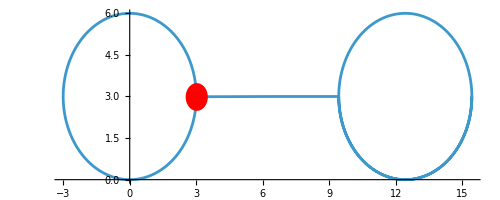
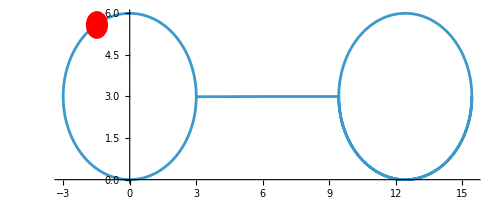
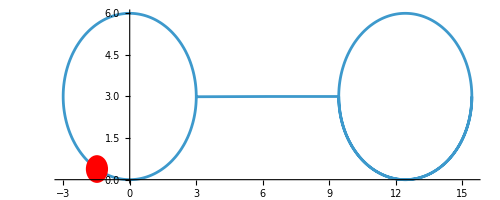
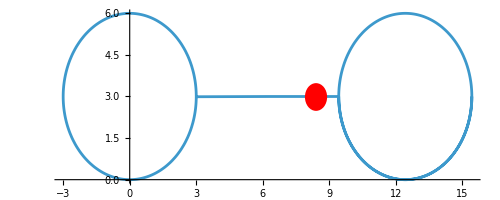
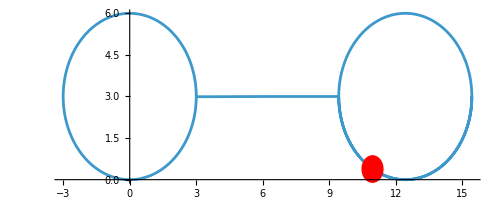
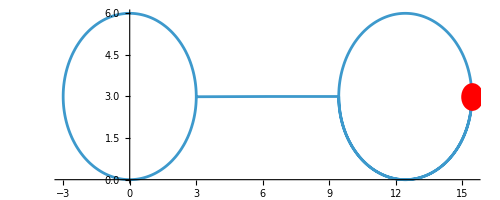
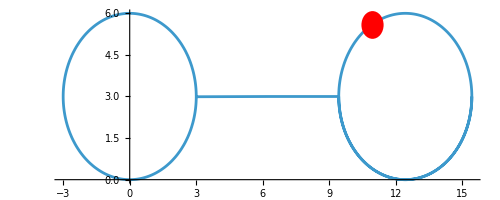
{,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
{Manipulate[Show[objpath4,Graphics[{Red,Disk[path4[t],1/2]},Axes->True]],{t,0,6*Pi}],
Table[Show[objpath4,Graphics[{Red,Disk[path4[t],1/2]},Axes->True]],{t,0,6*Pi,Pi/1.5}]}
```

```mathematica
(* Ladder *)
```

```mathematica
Ladder={{1,1},{5,5},{9,9},{13,13},{17,17},{21,21},{24,21},{28,17},{32,13},{36,9},{40,5}};
```

```mathematica
maxx=Max[Transpose[Ladder][[1]]];
```

```mathematica
{fncladder=Interpolation[Ladder,InterpolationOrder->0],
Interpolation[Ladder,InterpolationOrder->1]}
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
path5=ParametricPlot[{t,fncladder[t]},{t,1,maxx}]
```

-Graphics-

```mathematica
Manipulate[Show[{Graphics[{Red,RegularPolygon[{t,fncladder[t]},5,3]},PlotRange->{{-5,45},{0,25}},Axes->True],path5}],{t,1,maxx}]
```

```mathematica
(* Lecture Practice *)
```

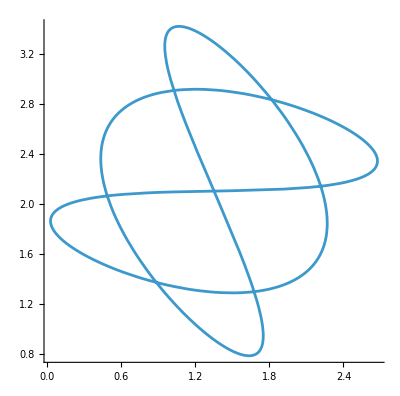
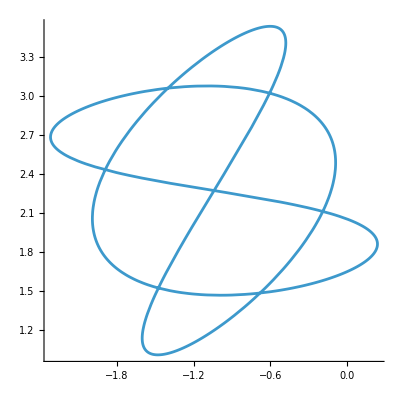
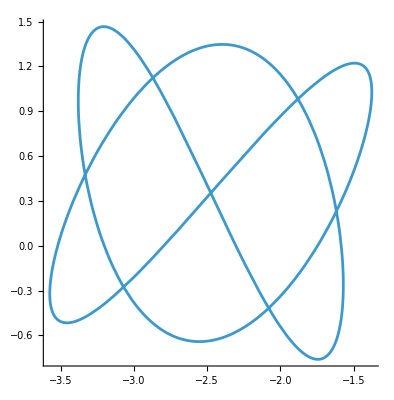

```mathematica
CurveGr1=ParametricPlot[{Sin[2*t],Cos[3*t]},{t,0,2*Pi}][[1]];
Cir1={Blue,Thick,Circle[{0,0},1.5]};
Tri1={RegularPolygon[{0,0},1.5,3]};
Pen1={RegularPolygon[{0,0},1.5,5]};
Lin1={Red,Thick,Line[{{-1,0},{1,0}}]};
k=1;Menu1=PopupMenu[Dynamic[k],{1->"Curve",2->"Circle",3->"Triangle",4->"Pentagon",5->"Line"}];
objlist1={CurveGr1,Cir1,Tri1,Pen1,Lin1};
GeoObj1[a_]:=GeometricTransformation[objlist1[[k]],Composition[RotationTransform[a],TranslationTransform[{2.5,0}]]]
{Manipulate[Dynamic[Graphics[GeoObj1[a],PlotRange->5,Axes->True]],{a,0,2*Pi}],{Menu1,Dynamic[k]},
Table[Graphics[GeoObj1[i],PlotRange->5,Axes->True],{i,1,3}]}
```

```mathematica
R=1;R1=5;R2=3.5;
points2[t_]:={R1*Cos[t],R2*Sin[t],5.5}
ecl=ParametricPlot3D[points2[t],{t,0,2*Pi},PlotRange->{{-6,6},{-6,6},{2.5,8}}];
sph[t_]:=ParametricPlot3D[{R*Cos[u]*Sin[v],R*Sin[u]*Sin[v],R*Cos[v]}+points2[t],{u,0,2*Pi},{v,0,2*Pi}]
arr=Graphics3D[{{Red,Arrow[{{0,0,5.5},{R1,0,5.5}}]},{Red,Arrow[{{0,0,5.5},{0,R2,5.5}}]}}];
{Manipulate[Show[ecl,sph[t],arr],{t,0,2*Pi}],
Table[Show[ecl,sph[t],arr],{t,0,Pi,Pi/2}]}
```

{,{-Graphics3D-,-Graphics3D-,-Graphics3D-}}

```mathematica
S[u_,v_]:={(v+2)*Cos[u],(v+2)*Sin[u],0.3*(u-v)};
objpara=ParametricPlot3D[S[u,v],{u,0,4*Pi},{v,0,6},Mesh->True,MeshStyle->Blue,PlotPoints->30,PlotStyle->{Orange,Specularity[5],Opacity[0.5]}];
objgraphics=objpara[[1]];
anc={0,0,0};
objrotate[a_,b_]:=GeometricTransformation[objgraphics,Composition[TranslationTransform[anc],RotationTransform[a,{0,0,1}],RotationTransform[b,{1,0,0}]]];
colors=RandomColor[12];
Manipulate[Graphics3D[{objrotate[a,b],{c,Sphere[anc,1]}},PlotRange->10,Axes->True,AxesOrigin->{0,0,0}],{a,0,2*Pi},{b,0,2*Pi},{c,colors}]
```

```mathematica
obj11=Cube[1.6];
obj2=Dodecahedron[1];
obj3=ParametricPlot3D[{u,v,u*v},{u,-1,1},{v,-1,1}][[1]];
objlist={obj11->"Cube",obj2->"Dodecahedron",obj3->"Surface"};
rotatelist={{1,0,0}->"x-axis",{0,1,0}->"y-axis",{0,0,1}->"z-axis"};
objrotate2[o_,a_,ax_]:=GeometricTransformation[o,RotationTransform[a,ax]]
Graphics3D[objrotate2[obj3,Pi/3,{1,0,0}]];
Manipulate[Graphics3D[objrotate2[o,a,ax],PlotRange->2],{o,objlist,ControlType->PopupMenu},{ax,rotatelist,ControlType->PopupMenu},{a,0,2*Pi}]
```

```mathematica
tor=Torus[{0,0,0},{4,8}];
Graphics3D[{Red,tor}];
Graphics3D[tor];
sph1={Blue,Sphere[{0,0,0},1.3]};
Graphics3D[sph1];
cen={Green,Icosahedron[{0,0,0}]};
Graphics3D[{Green,cen}];
rot1[a_]:=GeometricTransformation[sph1,Composition[RotationTransform[a,{0,0,1}],TranslationTransform[{8,0,0}]]]
rot2[a_,b_,c_]:=GeometricTransformation[{{c,Opacity[0.8],tor},rot1[a]},RotationTransform[b,{0,1,0}]]
Manipulate[Graphics3D[{rot2[a,b,c],cen},PlotRange->12],{a,0,2*Pi},{b,0,2*Pi},{c,RandomColor[10]}]
```

```mathematica
knot=ParametricPlot3D[{Sin[u]+2*Sin[2*u],Cos[u]-2*Cos[2*u],-Sin[3*u]},{u,0,2*Pi},PlotStyle->{Blue,Thickness[0.02]}];
knotgraaphics=knot[[1]];
piece[k_]:=ParametricPlot3D[{Sin[u]+2*Sin[2*u],Cos[u]-2*Cos[2*u],-Sin[3*u]},{u,k,k+0.2},PlotStyle->{Red,Thickness[0.03]}]
knotall[k_]:=Show[knot,piece[k]]
Table[knotall[i],{i,1,10}];
knotgraphics[k_]:=knotall[k][[1]]
Manipulate[Graphics3D[{{Green,PointSize[0.03],Point[{0,0,0}]},GeometricTransformation[knotgraphics[t],RotationTransform[t,{0,0,1}]]},PlotRange->3,Axes->True],{t,0,2*Pi}]
```